### Properties of the Coupled Gaussian

Examination of the ability of the κ, σ, q, and β parameters to provide interpretations of the properties of the distribution. In this analysis μ = 0 is assumed for simplicity. From analysis of the generalized mean, it is known that x = σ is significant because f(σ) = f_(κ-avg)(x). It’s further established that x = σ is the point where the derivative of the distribution on a log-log scale is equal to -1. Also, the point where the log-log derivative is one-half its asymptotic derivative is equal to σ/(√κ).

As the results below show, the minimum of the derivative (inflection point) and the maximum of the second derivative, also have relatively simple relationships with the σ and κ. While x=1/√βappears to be very close to the maximum of the second derivative, the functional relationship is quite complicated.

2nd Derivative: f’’(± σ/(√(1+2κ)))=0; f''(1/(√(β(1+q))))=0
Third Derivative: f’’’(± (√3 σ)/(√(1+2κ)))=0; f'''((√3)/(√(β(1+q))))=0

#### Examination of Derivative of Log-Log of Coupled Gaussian

```mathematica
FullSimplify[(x D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],0<κ<∞&&0<σ<∞&&x∈Reals],{x,1}])/PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals]
```

```mathematica
-(x^2 (1+κ))/(x^2 κ+σ^2)
```

```mathematica
Limit[-(x^2 (1+κ))/(x^2 κ+σ^2),x->∞]
```

(-1-κ)/κ

```mathematica
FullSimplify[Solve[(-1-κ)/(2κ)==-(x^2 (1+κ))/(x^2 κ+σ^2),x],0<κ<∞&&0<σ<∞&&-∞<u<∞]
```

{{x→-σ/(√κ)},{x→σ/(√κ)}}

```mathematica
-(x^2 (1+κ))/(x^2 κ+σ^2)/.x->{σ,σ/√κ,σ/√(1+κ),σ/√(1+2κ),σ/κ}//FullSimplify
```

{-1,-(1+κ)/(2 κ),-(1+κ)/(1+2 κ),-(1+κ)/(1+3 κ),-1/κ}

```mathematica
(-1-κ)/κ/.κ->0.1
```

-11.

Translation to q-statistics

```mathematica
betaQToScale[β,q]/(√qToCoupling[q])//FullSimplify
```

(√(1/(3 β-q β)))/(√(-1-2/(-3+q)))

```mathematica
(√(1/(3 β-q β)))/(√((q-1)/(3-q)))
```

```mathematica
√(1/(3 β(q-1)))
```

```mathematica
((1+ qToCoupling[q])/((q-1)β))^(1/2)//FullSimplify
```

√2 √(-1/((3-4 q+q^2) β))

```mathematica
√(2/((q-3)(1-q) β))
```

```mathematica
Manipulate[
domain={0.01,10};
PDFRange={{0.01,10},{10^-3,10}};
DerRange={-5,0.1};
scale=betaQToScale[β,q,2];
PDFValues=PDF[CoupledNormalDistribution[0,σ,κ],#]&/@{σ,σ/√κ};
DerValues=-(x^2 (1+κ))/(x^2 κ+σ^2)/.x->{σ,σ/√κ};
GraphicsRow[{
LogLogPlot[PDF[CoupledNormalDistribution[0,σ,κ],x],{x,domain[[1]],domain[[2]]},
PlotRange->PDFRange,
AxesLabel->{"x","f(x)"},
Epilog->{
{Black,PointSize[Large],
Point[Log@{σ,PDFValues[[1]]}],
Text["σ",Log@{σ,PDFValues[[1]]}+Log@{1.5,1.5}]},
{Red,PointSize[Large],
Point[Log@{σ/√κ,PDFValues[[2]]}],
Text["σ/(√κ)",Log@{σ/√κ,PDFValues[[2]]}-Log@{1.5,2.5}]}
}],
Plot[{-(x^2 (1+κ))/(x^2 κ+σ^2),Style[-1,Black,Dashed]},
{x,domain[[1]],domain[[2]]},
PlotRange->DerRange,
AxesLabel->{"x = ⅇ^u","g'(u)=ⅇ^u/(f (SuperscriptBox[ⅇ, u]))"},
Epilog->{
{Black,PointSize[Large],
Point[{σ,DerValues[[1]]}],
Text["σ",{σ,DerValues[[1]]}+{0.4,0.2}]},
{Red,PointSize[Large],
Point[{σ/(√κ),DerValues[[2]]}],
Text["σ/(√κ)",{σ/(√κ),DerValues[[2]]}-{0.4,0.8}]}
}]
}],
{{σ,1},0.1,5,Appearance->"Labeled"},
{{κ,0.5},0.1,5,Appearance->"Labeled"}]
```

#### Plot of PDF and Derivatives of PDF

```mathematica
Manipulate[
domain={0.01,10};
PDFRange={10^-3,10};
DerRange={-0.1,1};
scale=betaQToScale[β,q,2];
PDFValues=PDF[CoupledNormalDistribution[0,σ,κ],#]&/@{1/√scaleShapeToBeta[σ,κ],σ,σ/√(1+2κ),√3 σ/√(1+2κ)};
DerValues=FullSimplify[D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals],
{x,2}]]/.x->{1/√scaleShapeToBeta[σ,κ],σ,σ/√(1+2κ),√3 σ/√(1+2κ)};
GraphicsRow[{
LogLogPlot[PDF[CoupledNormalDistribution[0,σ,κ],x],{x,PDFRange[[1]],PDFRange[[2]]},
PlotRange->PDFRange,
AxesLabel->{"x","f(x)"},
Epilog->{
(*{Black,PointSize[Large],
Point[Log@{1/√scaleShapeToBeta[σ,κ],PDFValues[[1]]}],
Text["1/√β",Log@{1/√scaleShapeToBeta[σ,κ],PDFValues[[1]]}+Log@{1.5,1.5}]}, *){Black,PointSize[Large], 
Point[Log@{σ,PDFValues[[2]]}],
Text["σ",Log@{σ,PDFValues[[2]]}+Log@{1.5,1.5}]}, 
{Orange,PointSize[Large],
Point[Log@{σ/√(1+2κ),PDFValues[[3]]}],
Text["IP",Log@{σ/√(1+2κ),PDFValues[[3]]}+Log@{1.5,1.5}]},
{Red,PointSize[Large],
Point[Log@{√3 σ/√(1+2κ),PDFValues[[4]]}],
Text["derIP",Log@{√3 σ/√(1+2κ),PDFValues[[4]]}+Log@{1.8,1.5}]}
}],
Plot[Evaluate@D[PDF[CoupledNormalDistribution[0,σ,κ],x],{x,2}],
{x,domain[[1]],domain[[2]]},
PlotRange->DerRange,
AxesLabel->{"x","d^2f(x)/dx^2"},
Epilog->{
(*{Black,PointSize[Large],
Point[{1/√scaleShapeToBeta[σ,κ],DerValues[[1]]}],
Text["1/√β",{1/√scaleShapeToBeta[σ,κ],DerValues[[1]]}+{0.25,-0.1}]}, *)
{Black,PointSize[Large],
Point[{σ,DerValues[[2]]}],
Text["σ",{σ,DerValues[[2]]}+{-0.3,0.015}]}, 
{Orange,PointSize[Large],
Point[{σ/√(1+2κ),DerValues[[3]]}],
Text["IP",{σ/√(1+2κ),DerValues[[3]]}+{0.3,-0.02}]},
{Red,PointSize[Large],
Point[{√3 σ/√(1+2κ),DerValues[[4]]}],
Text["derIP",{√3 σ/√(1+2κ),DerValues[[4]]}+{0.4,0.015}]}
}]
}],
{{σ,2},0.5,5,Appearance->"Labeled"},
{{κ,1},10^-6,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
domain={0.01,10};
PDFRange={10^-3,10};
DerRange={-0.1,0.5};
scale=betaQToScale[β,q,2];
invBetaSqrt=1/√β;
PDFValues=PDF[qNormalDistribution[0,β,q],#]&/@{1/√β,betaQToScale[β,q],betaQToScale[β,q]/(√(1+2qToCoupling[q])),(√3 betaQToScale[β,q])/(√(1+2qToCoupling[q]))};
DerValues=FullSimplify[D[FullSimplify[PDF[qNormalDistribution[0,β,q],x],
1<q<3&&0<β<∞&&x∈Reals],
{x,2}]]/.x->{1/√β,betaQToScale[β,q],betaQToScale[β,q]/(√(1+2qToCoupling[q])),(√3 betaQToScale[β,q])/(√(1+2qToCoupling[q]))};
GraphicsRow[{
LogLogPlot[PDF[qNormalDistribution[0,β,q],x],{x,PDFRange[[1]],PDFRange[[2]]},
PlotRange->PDFRange,
AxesLabel->{"x","f(x)"},
Epilog->{
(*{Black,PointSize[Large],Point[Log@{1/√β,PDFValues[[1]]}],
Text["1/√β",Log@{1/√β,PDFValues[[1]]}+Log@{2,1.5}]},{Red,PointSize[Large],Point[Log@{betaQToScale[β,q],PDFValues[[2]]}],
Text["σ",Log@{betaQToScale[β,q],PDFValues[[2]]}+Log@{1.5,1.5}]}, *)
{Orange,PointSize[Large],
Point[Log@{betaQToScale[β,q]/(√(1+2qToCoupling[q])),PDFValues[[3]]}],
Text["IP",Log@{betaQToScale[β,q]/(√(1+2qToCoupling[q])),PDFValues[[3]]}+Log@{1.5,1.5}]},
{Red,PointSize[Large],
Point[Log@{(√3 betaQToScale[β,q])/(√(1+2qToCoupling[q])),PDFValues[[4]]}],
Text["derIP",Log@{betaQToScale[β,q]/(√(1+2qToCoupling[q])),PDFValues[[4]]}+Log@{1.5,1.5}]}
}],
Plot[Evaluate@D[PDF[qNormalDistribution[0,β,q],x],{x,2}],
{x,domain[[1]],domain[[2]]},
PlotRange->DerRange,
AxesLabel->{"x","d^2f(x)/dx^2"},
Epilog->{
(*{Black,PointSize[Large],
Point[{1/√β,DerValues[[1]]}],
Text["1/√β",{1/√β,DerValues[[1]]}+{0.5,-0.01}]},
{Red,PointSize[Large],
Point[{betaQToScale[β,q],DerValues[[2]]}],
Text["σ",{betaQToScale[β,q],DerValues[[2]]}+{0.3,-0.01}]}, *)
{Orange,PointSize[Large],
Point[{betaQToScale[β,q]/(√(1+2qToCoupling[q])),DerValues[[3]]}],
Text["IP",{betaQToScale[β,q]/(√(1+2qToCoupling[q])),DerValues[[3]]}+{0.3,-0.01}]},
{Red,PointSize[Large],
Point[{(√3 betaQToScale[β,q])/(√(1+2qToCoupling[q])),DerValues[[4]]}],
Text["derIP",{(√3 betaQToScale[β,q])/(√(1+2qToCoupling[q])),DerValues[[4]]}+{0.3,-0.01}]}
}]
}],
{{β,0.5},0.1,5,Appearance->"Labeled"},{{q,2},1+10^-6,2+2/3,Appearance->"Labeled"}]
```

Derivatives and Second Derivative

```mathematica
FullSimplify[D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals],
{x,1}]]
```

-(2 x κ Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2) Gamma[1/(2 κ)])

```mathematica
%/.x->σ/√(1+2κ)//FullSimplify
```

-(2 κ √(1+2 κ) Gamma[1/2 (3+1/κ)])/(√π (1+3 κ) √((1+κ/(1+2 κ))^(1+1/κ)/κ) σ^2 Gamma[1/(2 κ)])

```mathematica
-(2 x κ Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2) Gamma[1/(2 κ)])/.x->0
```

0

```mathematica
FullSimplify[D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals],
{x,2}]]
```

(2 κ (x^2 (1+2 κ)-σ^2) Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^2 Gamma[1/(2 κ)])

```mathematica
%/.x->σ/√(1+2κ)//FullSimplify
```

0

```mathematica
(2 κ (x^2 (1+2 κ)-σ^2) Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^2 Gamma[1/(2 κ)])/.x->0//FullSimplify
```

-(2 Gamma[1/2 (3+1/κ)])/(√π (1/κ)^(3/2) σ^3 Gamma[1/(2 κ)])

```mathematica
Limit[-(2 Gamma[1/2 (3+1/κ)])/(√π (1/κ)^(3/2) σ^3 Gamma[1/(2 κ)]),κ->0]
```

lim_(κ→0) -(2 Gamma[1/2 (3+1/κ)])/(√π (1/κ)^(3/2) σ^3 Gamma[1/(2 κ)])

```mathematica
Limit[(2 κ (x^2 (1+2 κ)-σ^2) Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^2 Gamma[1/(2 κ)]),κ->0]//FullSimplify
```

lim_(κ→0) (2 κ (x^2 (1+2 κ)-σ^2) Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^2 Gamma[1/(2 κ)])

Check 2nd derivative of the Gaussian

```mathematica
D[PDF[NormalDistribution[0,σ],x],{x,2}]//FullSimplify
```

(ⅇ^(-x^2/(2 σ^2)) (x-σ) (x+σ))/(√(2 π) σ^5)

```mathematica
(ⅇ^(-x^2/(2 σ^2)) (x-σ) (x+σ))/(√(2 π) σ^5)/.x->0//FullSimplify
```

-1/(√(2 π) σ^3)

```mathematica
Solve[(2 κ (x^2 (1+2 κ)-σ^2) Gamma[1/2 (3+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^2 Gamma[1/(2 κ)])==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-σ/(√(1+2 κ))},{x→σ/(√(1+2 κ))}}

```mathematica
FullSimplify[D[FullSimplify[PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals],
{x,3}]]
```

-(4 x κ^2 (x^2 (1+2 κ)-3 σ^2) Gamma[1/2 (5+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^3 Gamma[1/(2 κ)])

```mathematica
%/.x->1/√scaleShapeToBeta[σ,κ]//FullSimplify
```

-(4 √(2/π) κ^2 (-1+κ^2) √((1+κ)/σ^2) Gamma[1/2 (5+1/κ)])/(√((1+(2 κ)/(1+κ))^(1+1/κ)/κ) (σ+3 κ σ)^3 Gamma[1/(2 κ)])

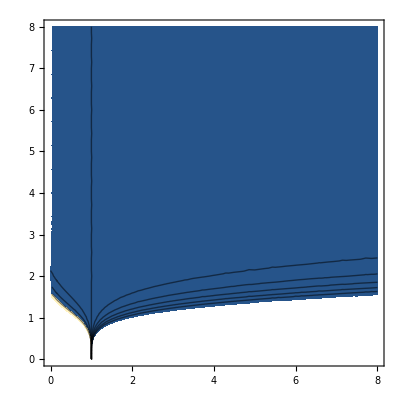

```mathematica
ContourPlot[-(4 √(2/π) κ^2 (-1+κ^2) √((1+κ)/σ^2) Gamma[1/2 (5+1/κ)])/(√((1+(2 κ)/(1+κ))^(1+1/κ)/κ) (σ+3 κ σ)^3 Gamma[1/(2 κ)]),{κ,0,8},{σ,0,8}]
```

```mathematica
Solve[-(4 x κ^2 (x^2 (1+2 κ)-3 σ^2) Gamma[1/2 (5+1/κ)])/(√π √(((1+(x^2 κ)/σ^2)^(1+1/κ))/κ) σ (x^2 κ+σ^2)^3 Gamma[1/(2 κ)])==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0},{x→-(√3 σ)/(√(1+2 κ))},{x→(√3 σ)/(√(1+2 κ))}}

```mathematica
FullSimplify[PDF[qNormalDistribution[0,β,q],x],1<q<3&&0<β<∞&&x∈Reals]
```

(√((-1+q) β) (1+(-1+q) x^2 β)^(1/(1-q)) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])

```mathematica
D[FullSimplify[PDF[qNormalDistribution[0,β,q],x],1<q<3&&0<β<∞&&x∈Reals],{x,2}]//FullSimplify
```

(2 β √((-1+q) β) (1+(-1+q) x^2 β)^(-2+1/(1-q)) (-1+(1+q) x^2 β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])

```mathematica
Solve[(2 β √((-1+q) β) (1+(-1+q) x^2 β)^(-2+1/(1-q)) (-1+(1+q) x^2 β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])==0,x]//FullSimplify
```

{{x→(√β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))}}

```mathematica
D[FullSimplify[PDF[qNormalDistribution[0,β,q],x],1<q<3&&0<β<∞&&x∈Reals],{x,3}]//FullSimplify
```

-(4 q x β^2 √((-1+q) β) (1+(-1+q) x^2 β)^(-3+1/(1-q)) (-3+(1+q) x^2 β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])

```mathematica
Solve[-(4 q x β^2 √((-1+q) β) (1+(-1+q) x^2 β)^(-3+1/(1-q)) (-3+(1+q) x^2 β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])==0,x]//FullSimplify
```

{{x→(√3 √q β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√(q (1+q) β^3 √((-1+q) β) Gamma[1/(-1+q)]))}}

```mathematica
(%156/.x->1/(√β))//FullSimplify
```

-(4 (-2+q) q^(-2+1/(1-q)) β^(3/2) √((-1+q) β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])

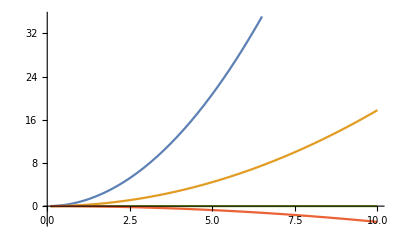

```mathematica
Plot[Evaluate[-(4 (-2+q) q^(-2+1/(1-q)) β^(3/2) √((-1+q) β) Gamma[1/(-1+q)])/(√π Gamma[-1/2+1/(-1+q)])/.q->{1+10^-6,1.5,2,2.5}],{β,0.1,10}]
```

Simplification of Inflection Point (value at which 2nd derivative is zero)

```mathematica
(√β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))//FullSimplify
```

(√β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))

```mathematica
(((-1+q) β^3)^(1/4))/((-1+q)^(1/4)β^(5/4)√(1+q))
```

```mathematica
1/(√(β(1+q)))
```

```mathematica
1/(√(β(1+q)))==(√β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))
```

1/(√((1+q) β))==(√β ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))

Simplification of value at which third derivative is zero

```mathematica
(√(3β) ((-1+q) β)^(1/4) √Gamma[1/(-1+q)])/(√((1+q) β^2 √((-1+q) β) Gamma[1/(-1+q)]))
```

```mathematica
(√3)/(√((1+q) β))
```

#### Role of alpha - curvature at x = μ?

### Properties of Coupled Exponential

```mathematica
Manipulate[
domain={0.001,10};
PDFRange={10^-4,1000};
DerRange={-2,2};
PDFValues=PDF[CoupledExponentialDistribution[0,σ,κ],#]&/@{σ,σ/κ};
DerValues=FullSimplify[(x D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledExponentialDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&0<x<∞]/.x->{σ,σ/κ};
GraphicsRow[{
LogLogPlot[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,PDFRange[[1]],PDFRange[[2]]},
PlotRange->PDFRange,
AxesLabel->{"x","f(x)"},
Epilog->{
{Red,PointSize[Large],
Point[Log@{σ,PDFValues[[1]]}],
Text["σ",Log@{σ,PDFValues[[1]]}+Log@{1.5,1.5}]},
{Orange,PointSize[Large],
Point[Log@{σ/κ,PDFValues[[2]]}],
Text["σ/κ",Log@{σ/κ,PDFValues[[2]]}+Log@{1.5,2.5}]}
}],
Plot[Evaluate@((x D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledExponentialDistribution[0,σ,κ],x]),
{x,domain[[1]],domain[[2]]},
PlotRange->DerRange,
AxesLabel->{"x","df(x)/dx"},
Epilog->{
{Red,PointSize[Large],
Point[{σ,DerValues[[1]]}],
Text["σ",{σ,DerValues[[1]]}+{0.25,-0.1}]},
{Orange,PointSize[Large],
Point[{σ/κ,DerValues[[2]]}],
Text["σ/κ",{σ/κ,DerValues[[2]]}+{0.25,-0.1}]}
}]
}],
{{σ,2},10^-6,5,Appearance->"Labeled"},
{{κ,1},10^-6,5,Appearance->"Labeled"}]
```

Determine derivative of log-log plot
https://math.stackexchange.com/questions/2820920/how-to-find-an-inflection-point-maximum-slope-of-a-log-log-plot

-Graphics-

Computation of the derivative of the log-log function of the coupled exponential distribution

```mathematica
FullSimplify[D[Log[PDF[CoupledExponentialDistribution[0,σ,κ],ⅇ^u]],{u,1}],0<κ<∞&&0<σ<∞&&-∞<u<∞]
```

-(ⅇ^u (1+κ))/(ⅇ^u κ+σ)

```mathematica
-(ⅇ^u (1+κ))/(ⅇ^u κ+σ)/.u->Log[σ]//FullSimplify
```

-1

```mathematica
FullSimplify[D[PDF[CoupledExponentialDistribution[0,σ,κ],ⅇ^u],{u,1}]/PDF[CoupledExponentialDistribution[0,σ,κ],ⅇ^u],0<κ<∞&&0<σ<∞&&-∞<u<∞]
```

-(ⅇ^u (1+κ))/(ⅇ^u κ+σ)

```mathematica
-(ⅇ^u (1+κ))/(ⅇ^u κ+σ)/.u->Log[σ]//FullSimplify
```

-1

```mathematica
FullSimplify[D[PDF[CoupledExponentialDistribution[0,σ,κ],ⅇ^u],{u,1}],0<κ<∞&&0<σ<∞&&-∞<u<∞]
```

-ⅇ^u (1+κ) σ^(1/κ) (ⅇ^u κ+σ)^(-2-1/κ)

The derivation below seems to have a mistake. I shouldn’t have substituted x = e^u.

```mathematica
FullSimplify[(x D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledExponentialDistribution[0,σ,κ],x],0<κ<∞&&0<σ<∞&&0<x<∞]
```

-(x (1+κ))/(x κ+σ)

```mathematica
-(x (1+κ))/(x κ+σ)/.x->σ//FullSimplify
```

-1

```mathematica
Limit[-(x (1+κ))/(x κ+σ),x->∞]
```

(-1-κ)/κ

```mathematica
Solve[(-1-κ)/(2κ)==-(x (1+κ))/(x κ+σ),x]
```

{{x→σ/κ}}

```mathematica
-(x (1+κ))/(x κ+σ)/.x->σ/κ//FullSimplify
```

-(1+κ)/(2 κ)

Show Derivative of Coupled Exponential Distribution

```mathematica
D[PDF[CoupledExponentialDistribution[0,σ,κ],x],{x,1}]//FullSimplify
```

Piecewise[{{-ⅇ^(-x/σ)/σ^2, κ==0&&x>0&&σ≠0}, {-((1+κ) (1+(x κ)/σ)^(-1/κ))/(x κ+σ)^2, (κ≥0||κ (x κ+σ)<0)&&x>0&&σ (x κ+σ)>0}, {0, True}}]

```mathematica
Clear[LogLog2ndDer];
LogLog2ndDer[f_,u_]:=1/(f[ⅇ^u]^2)(f[ⅇ^u](D[f[ⅇ^u],{x,2}] ⅇ^(2u)-D[f[ⅇ^u],{x,1}] ⅇ^u)-D[f[ⅇ^u],{x,1}]^2 ⅇ^(2u));
```

```mathematica
LogLog2ndDer[PDF[CoupledExponentialDistribution[0,σ,κ],#]&,Log[x]]//FullSimplify
```

Piecewise[{{x/σ, κ==0&&x>0&&σ≠0}, {(x (1+κ) (2 x κ+σ))/(x κ+σ)^2, x>0&&σ (x κ+σ)>0&&(κ≥0||κ (x κ+σ)<0)}, {ComplexInfinity, x>0&&σ (x κ+σ)>0&&((κ<-1&&κ (x κ+σ)<0)||κ>0)}, {Indeterminate, True}}]

```mathematica
LogLog2ndDer[1/NormCG[σ,κ](CoupledExponential[(#-0)^2/σ^2,κ])^(-1/2)&,Log[x]]//FullSimplify
```

Piecewise[{{(2 x^4 κ (1+κ))/((x^2 κ+σ^2)^2), κ==0||(x^2 κ)/σ^2>-1}, {Indeterminate, True}}]

```mathematica
LogLog2ndDer[(α (κ/(κ+Abs[(#-0)/σ]^-α))^(1/α) (1/(1+κ Abs[(#-0)/σ]^α))^(1/(α κ)) Abs[σ] Abs'[(#-0)/σ])/(2 σ Abs[#-0] Beta[1/α,1/(α κ)])&,Log[x]]//FullSimplify
```

LogLog2ndDer[(α (κ/(κ+Abs[(#1+0)/σ]^-α))^(1/α) (1/(1+κ Abs[(#1+0)/σ]^α))^(1/(α κ)) Abs[σ] Abs'[(#1+0)/σ])/(2 σ Abs[#1+0] Beta[1/α,1/(α κ)])&,Log[x]]

```mathematica
FullSimplify[%109/.{x->0,x->σ},0<σ<∞&&0<α<∞&&0<κ<∞]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
FullSimplify[Abs'[x]/.x->σ,0<σ<∞]
```

1

CDF of Coupled Distribution

```mathematica
Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], x≤μ}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}]
```

Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], x≤μ}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}]

Survival Function of Coupled Distribution

```mathematica
Clear[SFCoupledDistribution];SFCoupledDistribution[x_,μ_,σ_,κ_,α_]:=Piecewise[{{1-1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], x≤μ}, {1/2(1-BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}];
```

```mathematica
Clear[LogLogDerSFCD];LogLogDerSFCD[x_,μ_,σ_,κ_,α_]:=(x D[SFCoupledDistribution[x,μ,σ,κ,α],{x,1}])/SFCoupledDistribution[x,μ,σ,κ,α];
```

```mathematica
FullSimplify[LogLogDerSFCD[x,0,σ,κ,α],0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

$Aborted

```mathematica
FullSimplify[LogLogDerSFCD[x,0,σ,κ,1],0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

-x/(x κ+σ)

```mathematica
FullSimplify[LogLogDerSFCD[x,0,σ,κ,2],0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

(2 x √κ σ^(1/κ) (x^2 κ+σ^2)^(-(1+κ)/(2 κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[(x^2 κ)/(x^2 κ+σ^2),1/2,1/(2 κ)]))

```mathematica
LogLogDerSFCD[x,0,σ,κ,α]/.x->σ//FullSimplify
```

(α (1/(1+κ))^(1/(α κ)) (κ/(1+κ))^(1/α))/(Beta[1/α,1/(α κ)] (-1+BetaRegularized[κ/(1+κ),1/α,1/(α κ)]))

```mathematica
FullSimplify[(x α κ^(1/α) (1+κ (x/σ)^α)^(-(1+κ)/(α κ)))/(σ Beta[1/α,1/(α κ)] (-1+BetaRegularized[1-1/(1+κ (x/σ)^α),1/α,1/(α κ)]))/.x->σ/κ,0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

(α κ^(-1+1/α) (1+κ^(1-α))^(-(1+κ)/(α κ)))/(Beta[1/α,1/(α κ)] (-1+BetaRegularized[κ/(κ+κ^α),1/α,1/(α κ)]))

```mathematica
FullSimplify[(x α κ^(1/α) (1+κ (x/σ)^α)^(-(1+κ)/(α κ)))/(σ Beta[1/α,1/(α κ)] (-1+BetaRegularized[1-1/(1+κ (x/σ)^α),1/α,1/(α κ)]))/.x->σ,0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

(α κ^(1/α) (1+κ)^(-(1+κ)/(α κ)))/(Beta[1/α,1/(α κ)] (-1+BetaRegularized[κ/(1+κ),1/α,1/(α κ)]))

```mathematica
FullSimplify[(x α κ^(1/α) (1+κ (x/σ)^α)^(-(1+κ)/(α κ)))/(σ Beta[1/α,1/(α κ)] (-1+BetaRegularized[1-1/(1+κ (x/σ)^α),1/α,1/(α κ)]))/.x->σ/κ^(1/α),0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

(2^(-(1+κ)/(α κ)) α)/(Beta[1/α,1/(α κ)] (-1+BetaRegularized[1/2,1/α,1/(α κ)]))

```mathematica
(α (1/(1+κ))^(1/(α κ)) (κ/(1+κ))^(1/α))/(Beta[1/α,1/(α κ)] (-1+BetaRegularized[κ/(1+κ),1/α,1/(α κ)]))/.α->{1,2}//FullSimplify
```

{-1/(1+κ),(2 (1/(1+κ))^(1/2/κ) √(κ/(1+κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[κ/(1+κ),1/2,1/(2 κ)]))}

```mathematica
FullSimplify[Limit[(2 x √κ σ^(1/κ) (x^2 κ+σ^2)^(-(1+κ)/(2 κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[(x^2 κ)/(x^2 κ+σ^2),1/2,1/(2 κ)])),x->∞],0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

$Aborted

```mathematica
FullSimplify[Limit[(2 x √κ σ^(1/κ) (x^2 κ)^(-(1+κ)/(2 κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[1,1/2,1/(2 κ)])),x->∞],0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

Undefined

```mathematica
Solve[(2 x √κ σ^(1/κ) (x^2 κ+σ^2)^(-(1+κ)/(2 κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[(x^2 κ)/(x^2 κ+σ^2),1/2,1/(2 κ)]))==-1/(2κ),x,Reals,Assumptions->0<κ<∞&&0<σ<∞&&0<x<∞&&0<α<=2]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(2 x √κ σ^(1/κ) (x^2 κ+σ^2)^(-(1+κ)/(2 κ)))/(Beta[1/2,1/(2 κ)] (-1+BetaRegularized[(x^2 κ)/(x^2 κ+σ^2),1/2,1/(2 κ)]))==-1/(2 κ),x,ℝ,Assumptions→0<κ<∞&&0<σ<∞&&0<x<∞]

```mathematica
Manipulate[
domain={0.01,10};
PDFRange={10^-3,100};
DerRange={-1,0.1};
scale=betaQToScale[β,q,2];
PDFValues=PDF[CoupledNormalDistribution[0,σ,κ],#]&/@{1/√scaleShapeToBeta[σ,κ],σ,σ/√(1+2κ)};
DerValues=FullSimplify[(x D[PDF[CoupledNormalDistribution[0,σ,κ],x],{x,1}])/PDF[CoupledNormalDistribution[0,σ,κ],x],
0<κ<∞&&0<σ<∞&&x∈Reals]/.x->{1/√scaleShapeToBeta[σ,κ],σ,σ/√(1+2κ)};
GraphicsRow[{
LogLogPlot[SFCoupledDistribution[x,0,σ,κ,α],{x,PDFRange[[1]],PDFRange[[2]]},
PlotRange->PDFRange,
AxesLabel->{"x","f(x)"},
Epilog->{
{Black,PointSize[Large],
Point[Log@{1/√scaleShapeToBeta[σ,κ],PDFValues[[1]]}],
Text["1/√β",Log@{1/√scaleShapeToBeta[σ,κ],PDFValues[[1]]}+Log@{1.5,1.5}]},{Red,PointSize[Large],
Point[Log@{σ,PDFValues[[2]]}],
Text["σ",Log@{σ,PDFValues[[2]]}+Log@{1.5,1.5}]},
{Orange,PointSize[Large],
Point[Log@{σ/√(1+2κ),PDFValues[[3]]}],
Text["IP",Log@{σ/√(1+2κ),PDFValues[[3]]}+Log@{1.5,1.5}]}
}],
Plot[(x α κ^(1/α) (1+κ (x/σ)^α)^(-(1+κ)/(α κ)))/(σ Beta[1/α,1/(α κ)] (-1+BetaRegularized[1-1/(1+κ (x/σ)^α),1/α,1/(α κ)])),
{x,domain[[1]],domain[[2]]},
PlotRange->DerRange,
AxesLabel->{"x","df(x)/dx"},
Epilog->{
{Black,PointSize[Large],
Point[{1/√scaleShapeToBeta[σ,κ],DerValues[[1]]}],
Text["1/√β",{1/√scaleShapeToBeta[σ,κ],DerValues[[1]]}+{0.25,-0.1}]},
{Red,PointSize[Large],
Point[{σ,DerValues[[2]]}],
Text["σ",{σ,DerValues[[2]]}+{0.25,-0.1}]},
{Orange,PointSize[Large],
Point[{σ/√(1+2κ),DerValues[[3]]}],
Text["IP",{σ/√(1+2κ),DerValues[[3]]}+{0.25,-0.1}]}
}]
}],
{{σ,2},0.5,5,Appearance->"Labeled"},
{{κ,1},10^-6,5,Appearance->"Labeled"}]
```

### Definition of Stretched Coupled Distribution

```mathematica
Clear[α,CoupledDistribution]
```

```mathematica
CoupledDistribution[μ_,σ_,κ_,α_]:=
ProbabilityDistribution[{"CDF",Piecewise[{{1/2 BetaRegularized[1/(1+κ Abs[(x-μ)/σ]^α),1/(α κ),1/α], x≤μ}, {1/2 (1+BetaRegularized[(κ Abs[(x-μ)/σ]^α)/(1+κ Abs[(x-μ)/σ]^α),1/α,1/(α κ)]), True}}]},
{x,-∞,∞}];
```

```mathematica
FullSimplify[PDF[CoupledDistribution[μ,σ,κ,α],x],Assumptions->0<αα<∞&&0<κ<∞&&0<σ<∞&&0<μ<∞&&x>μ]
```

(α (1-1/(1+κ ((x-μ)/σ)^α))^(1/α) (1/(1+κ ((x-μ)/σ)^α))^(1/(α κ)))/(2 (x-μ) Beta[1/α,1/(α κ)])

Check Definition of Coupled Distribution for negative values of κ

```mathematica
FullSimplify[1/2 (1+BetaRegularized[-1/0,1/α,1/(α κ)]),
Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞&&0<μ<∞&&x>μ]
```

Power::infy: Infinite expression 1/0 encountered.

Indeterminate

```mathematica
Limit[1/2 (1+BetaRegularized[u,1/α,1/(α κ)]),u->0,
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&x>μ]
```

1/2 (1+(Beta[0,1/α,1/(α κ)] Gamma[(1+κ)/(α κ)])/(Gamma[1/α] Gamma[1/(α κ)]))

```mathematica
FullSimplify[1/2 (1+BetaRegularized[1,1/α,1/(α κ)]),Assumptions->0<α<∞&&0<κ<∞]
```

1

#### Coupled Distribution with negative coupling

Reference: 
Li, R., & Nadarajah, S. (2020). A review of Student’s t distribution and its generalizations. Empirical Economics, 58(3), 1461–1490. https://doi.org/10.1007/s00181-018-1570-0
https://pure.manchester.ac.uk/ws/portalfiles/portal/78743532/studentt.pdf

Examine expression in the Beta Function

```mathematica
FullSimplify[(κ-(κ-2)Sign[κ])/(4κ),Assumptions->κ>0]
```

1/(2 κ)

```mathematica
FullSimplify[(κ-(κ-2)Sign[κ])/(4κ),Assumptions->κ<0]
```

(-1+κ)/(2 κ)

```mathematica
FullSimplify[(κ-(κ-2)Sign[κ])/(4κ)]
```

(κ-(-2+κ) Sign[κ])/(4 κ)

```mathematica
(1/4-1/4 Sign[κ])+1/(2Abs[κ])//FullSimplify
```

(2-κ+Abs[κ])/(4 Abs[κ])

```mathematica
FullSimplify[(2-κ+Abs[κ])/(4 Abs[κ]),Assumptions->κ<0]
```

(-1+κ)/(2 κ)

```mathematica
FullSimplify[(2-κ+Abs[κ])/(4 Abs[κ]),Assumptions->κ>0]
```

1/(2 κ)

```mathematica
(1/(2α)-1/(2α)Sign[κ])+1/(α Abs[κ])//FullSimplify
```

(2-κ+Abs[κ])/(2 α Abs[κ])

So the normalization of the Coupled Gaussian Distribution can be defined more simply to be

```mathematica
ZCG[σ_,κ_]:=Piecewise[{{√(2 π) σ, κ==0}, {σ Beta[1/2,(2-κ+Abs[κ])/(4 Abs[κ])]/(√Abs[κ]), True}}]
```

```mathematica
FullSimplify[∫_(-∞)^∞ FullSimplify[((CoupledExponential[(x)^2/σ^2,κ])^(-1/2))/ZCG[σ,κ],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&κ∈Reals&&σ∈Reals]ⅆx,
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

1

```mathematica
FullSimplify[∫_(-√(σ^2/Abs[κ]))^(+√(σ^2/Abs[κ])) FullSimplify[((CoupledExponential[(x)^2/σ^2,κ])^(-1/2))/ZCG[σ,κ],
Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞&&κ∈Reals&&σ∈Reals]ⅆx,
Assumptions->0<α<∞&&-1<κ<0&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

Integrate::pwrl: Unable to prove that integration limits {-(√(σ^2))/(√Abs[κ]),(√(σ^2))/(√Abs[κ])} are real. Adding assumptions may help.

1

```mathematica
FullSimplify[∫FullSimplify[((CoupledExponential[(x)^2/σ^2,κ])^(-1/2))/ZCG[σ,κ],
Assumptions->0<α<∞&&κ!=0&&0<σ<∞&&κ∈Reals&&σ∈Reals]ⅆx,
Assumptions->0<α<∞&&κ!=0&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

Piecewise[{{ComplexInfinity, κ<-1&&x^2 κ+σ^2≤0}, {0, κ≥-1&&x^2 κ+σ^2≤0}, {(x (x^2 κ+σ^2)^(-(1+κ)/(2 κ)) √(κ (x^2 κ+σ^2)^(1+1/κ)) Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-(x^2 κ)/σ^2])/(σ Beta[1/2,1/(2 κ)]), κ≥0}, {(x √-κ Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-(x^2 κ)/σ^2])/(σ Beta[1/2,(-1+κ)/(2 κ)]), True}}]

```mathematica
Piecewise[{{(x √κ Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-(x^2 κ)/σ^2])/(σ Beta[1/2,1/(2 κ)]), κ≥0}, {(x √-κ Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-(x^2 κ)/σ^2])/(σ Beta[1/2,(-1+κ)/(2 κ)]), -1<=κ<0}}]
```

```mathematica
(x √Abs[κ] Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-((x-μ)^2 κ)/σ^2])/(σ Beta[1/2,(2-κ+Abs[κ])/(4 Abs[κ])])
```

```mathematica
FullSimplify[Limit[(x √Abs[κ] Hypergeometric2F1[1/2,(1+κ)/(2 κ),3/2,-((x-μ)^2 κ)/σ^2])/(σ Beta[1/2,(2-κ+Abs[κ])/(4 Abs[κ])]),
x->∞,Assumptions->0<α<∞&&κ!=0&&κ>0&&0<σ<∞&&κ∈Reals&&σ∈Reals],Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

1/2

#### Determine generalization with α

```mathematica
FullSimplify[(x √Abs[κ] Hypergeometric2F1[1/2,(1+κ)/(α κ),3/α,-∞])/(σ Beta[1/2,(2-κ+Abs[κ])/(2α Abs[κ])]),Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

(x √Abs[κ] Hypergeometric2F1[1/2,(1+κ)/(α κ),3/α,-∞])/(σ Beta[1/2,(2-κ+Abs[κ])/(2 α Abs[κ])])

Leave out the Beta function since I don’t know how that generalizes

```mathematica
FullSimplify[Limit[(x Abs[κ]^(1/α) Hypergeometric2F1[1/2,(1+κ)/(α κ),3/2,-((x-μ)^α κ)/σ^α])/σ,
x->∞,Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals],Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

ConditionalExpression[ⅇ^(-(ⅈ π (1+κ))/(α κ)) ∞, μ∈ℝ&&κ<0]

```mathematica
FullSimplify[Limit[(x Abs[κ]^(1/α) Hypergeometric2F1[1/2,(1+κ)/(α κ),3/α,-((x-μ)^α κ)/σ^α])/σ,
x->∞,Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals],Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

ConditionalExpression[ⅇ^(-(ⅈ π (1+κ))/(α κ)) ∞, μ∈ℝ&&κ<0]

```mathematica
FullSimplify[Limit[(x Abs[κ]^(1/α) Hypergeometric2F1[1/2,(1+κ)/(α κ),3/2,-((x-μ)^α κ)/σ^α])/(σ Beta[1/2,(2-κ+Abs[κ])/(2 α Abs[κ])]),
x->∞,Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals],Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

ConditionalExpression[ⅇ^(-(ⅈ π (1+κ))/(α κ)) ∞, μ∈ℝ&&κ<0]

```mathematica
FullSimplify[Limit[(x Abs[κ]^(1/α) Hypergeometric2F1[1/2,(1+κ)/(α κ),3/2,-((x-μ)^α κ)/σ^α])/(σ Beta[1/2,(α+(α-1)(-κ+Abs[κ]))/(2 α Abs[κ])]),
x->∞,Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals],Assumptions->0<α<∞&&κ!=0&&κ>0&&0<σ<∞&&κ∈Reals&&σ∈Reals]
```

Undefined

Try using Regularized Incomplete Beta function as a starting point

```mathematica
CoupledDistribution[μ_,σ_,κ_,α_]:=
Module[{x},
ProbabilityDistribution[{"CDF",Piecewise[{{1/2 BetaRegularized[1/(1+κ ComplexExpand[Abs[(x-μ)/σ]^α]),1/(α κ),1/α], x≤μ}, {1/2 (1+BetaRegularized[(κ ComplexExpand[Abs[(x-μ)/σ]^α])/(1+κ ComplexExpand[Abs[(x-μ)/σ]^α]),1/α,1/(α κ)]), True}}]},
{x,-∞,∞},
Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals&&x∈Reals&&μ∈Reals&&α∈Reals]
];
```

```mathematica
PDF[CoupledDistribution[0,1,-0.5,1.5],1]
```

0.144949-0.25106 ⅈ

```mathematica
CDF[CoupledDistribution[0,1,-0.5,1.5],10]
```

7.03167-12.1792 ⅈ

```mathematica
CDF[CoupledDistribution[0,σ,-0.5,α],σ/0.5^(1/α)]//FullSimplify
```

$Aborted

```mathematica
ComplexExpand[Abs[x]]
```

√(x^2)

```mathematica
FullSimplify[PDF[CoupledDistribution[0,σ,κ,α],x],
Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals&&x∈Reals&&μ∈Reals&&α∈Reals]
```

ProbabilityDistribution::ignjmps: The distribution function of ProbabilityDistribution[{CDF,Piecewise[{{1/2 BetaRegularized[Power[«2»],Times[«2»],Power[«2»]], x$3279636≤0}, {1/2 (1+BetaRegularized[κ Power[«2»] Power[«2»],1/α,Power[«2»] Power[«2»]]), True}}]},{x$3279636,-∞,∞},Assumptions→0<α<∞&&κ≠0&&κ>-1&&0<σ<∞&&κ∈&&σ∈&&x$3279636∈&&α∈] has negative atomic weight. Proceeding by ignoring the discontinuities, which may result in non-normalized density function.

Piecewise[{{(α (κ/(x^α κ+σ^α))^(1/α) (σ^α/(x^α κ+σ^α))^(1/(α κ)))/(2 Beta[1/α,1/(α κ)]), x>0}, {(α σ^(1/κ) (1/((-x)^α κ+σ^α))^(1/(α κ)) (κ/((-x)^α κ+σ^α))^(1/α))/(2 Beta[1/(α κ),1/α]), True}}]

Attempt at CDF definition for negative values of κ

```mathematica
CoupledDistribution[μ_,σ_,κ_,α_]:=
Module[{x},
ProbabilityDistribution[{"CDF",Piecewise[{{1/2 BetaRegularized[1/(1+κ ComplexExpand[Abs[(x-μ)/σ]^α]),(2-κ+ComplexExpand[Abs[κ]])/(2 α ComplexExpand[Abs[κ]]),1/α], x≤μ}, {1/2 (1+BetaRegularized[(κ ComplexExpand[Abs[(x-μ)/σ]^α])/(1+κ ComplexExpand[Abs[(x-μ)/σ]^α]),1/α,(2-κ+ComplexExpand[Abs[κ]])/(2 α ComplexExpand[Abs[κ]])]), True}}]},
{x,-∞,∞},
Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals&&x∈Reals&&μ∈Reals&&α∈Reals]
];
```

```mathematica
PDF[CoupledDistribution[0,1,-0.5,1.5],1]
```

-1.66667+2.88675 ⅈ

```mathematica
CDF[CoupledNormalDistribution[0,1,-0.5],]
```

0.909155

```mathematica
FullSimplify[PDF[CoupledDistribution[0,σ,κ,α],x],
Assumptions->0<α<∞&&κ!=0&&κ>-1&&0<σ<∞&&κ∈Reals&&σ∈Reals&&x∈Reals&&μ∈Reals&&α∈Reals]
```

Piecewise[{{(α (κ/(x^α κ+σ^α))^(1/α) (σ^α/(x^α κ+σ^α))^((2-κ+Abs[κ])/(2 α Abs[κ])))/(2 Beta[1/α,(2-κ+Abs[κ])/(2 α Abs[κ])]), x>0}, {(α (κ/((-x)^α κ+σ^α))^(1/α) (σ^α/((-x)^α κ+σ^α))^((2-κ+Abs[κ])/(2 α Abs[κ])))/(2 Beta[(2-κ+Abs[κ])/(2 α Abs[κ]),1/α]), True}}]

### Maximum 2nd Derivative of Log-Log Plot of Coupled Distribution

Log[f[ⅇ^u]] is the Log-Log function of f[x]; where u = Log[x]

```mathematica
D[Log[f[ⅇ^u]],{u,1}]/.u->Log[x]//FullSimplify
```

(x f'[x])/f[x]

```mathematica
D[Log[f[ⅇ^u]],{u,2}]/.u->Log[x]//FullSimplify
```

(x (-x f'[x]^2+f[x] (f'[x]+x f''[x])))/f[x]^2

```mathematica
FullSimplify[
D[
FullSimplify[
Log[
FullSimplify[
PDF[CoupledDistribution[0,σ,κ,α],ⅇ^u],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
]
],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
],{u,2}]/.u->Log[x],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
]
```

-(α (1+κ) (x σ)^α)/((x^α κ+σ^α)^2)

```mathematica
-(α (1+κ) (x σ)^α)/((x^α κ+σ^α)^2)/.α->{1,2}//FullSimplify
```

{-(x (1+κ) σ)/(x κ+σ)^2,-(2 x^2 (1+κ) σ^2)/((x^2 κ+σ^2)^2)}

```mathematica
Minimize[-(α (1+κ) (x σ)^α)/((x^α κ+σ^α)^2),x]
```

Minimize[-(α (1+κ) (x σ)^α)/((x^α κ+σ^α)^2),x]

```mathematica
Manipulate[
Plot[{-(x (1+κ) σ)/(x κ+σ)^2,-(2 x^2 (1+κ) σ^2)/((x^2 κ+σ^2)^2)},{x,0,10}],
{σ,0.1,5},{κ,0.1,5}]
```

```mathematica
FullSimplify[
D[
FullSimplify[
Log[
FullSimplify[
PDF[CoupledDistribution[0,σ,κ,α],ⅇ^u],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
]
],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
],{u,3}]/.u->Log[x],
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals
]
```

(α^2 (1+κ) (x σ)^α (x^α κ-σ^α))/((x^α κ+σ^α)^3)

```mathematica
FullSimplify[
Solve[(α^2 (1+κ) (x σ)^α (x^α κ-σ^α))/((x^α κ+σ^α)^3)==0,x,
Assumptions->0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals&&x∈Reals],
0<α<∞&&0<κ<∞&&0<σ<∞&&0<x<∞&&u∈Reals&&x∈Reals
]
```

$Aborted

From observation (x^α κ-σ^α)determines where the third derivative is zero and therefore the minimum 2nd derivative.
So x = σ/κ^(1/α)is the maximum curvature and therefore the “knee of the curve”.  This is also the point where the derivative is halve the minimum, where the minimum is at limit x -> ∞.